### Modelling of 5-level system for Li^6

dipole matrix elements for spontaneous and induced processes

natural and saturation line widths

#### Constants & Functions

```mathematica
Clear[α, S, Is, I0, qe, h,τ, g,me, μ0, W,ν34, ν45, ν35, c, a1, a3];

λ=670.977 10^-9;
ϵ0=8.85 10^-12;
μ0=3.977 10^-29;
h=6.62607015 10^-34;
c=299792458;
νD2=c/λ;
a3 =1.1 10^6;
a1 = 152.1 10^6;
ν13 =-3/2 a3-a1
ν14=-a1
ν15 =5/2 a3-a1
ν23 =-3/2 a3+1/2 a1
ν24 =1/2 a1
ν25 =5/2 a3+1/2 a1
α=(16 π^3 ν^3)/(3 ϵ0 h c^3) μ0^2;
S=10;
τ = 27.1 10^-9;
Γ = 1/(2π τ)√(1+S);
g[v_, v0_] := 1/π  (Γ/2)/((Γ/2)^2+(v-v0)^2);
Is = 25.4;
I0 = Is   S;
me=9.1 10^-31;
μ0=3.977 10^-29;
qe=1.62 10^-19;
W[ν_, ν0_]:=8 me I0 ((Pi μ0)/(qe h))^2 g[ν, ν0];
```

-1.5375×10^8

-1.521×10^8

-1.4935×10^8

7.44×10^7

7.605×10^7

7.88×10^7

#### Rate equations

```mathematica
Clear[n1, n2, n3, n4, n5, eq, tp, sol, ν];

ν=ν14;

eq={
n1'[t]==(5α)/36 n4[t] + (2α)/9 n5[t] + W[ν, ν14](5/36 n4[t]-5/18 n1[t])+W[ν,ν15](2/9 n5[t]-2/9 n1[t]),
n2'[t]==α/4 n3[t] + α/9 n4[t]+α/36 n5[t] +W[ν, ν23](1/4 n3[t]-3/8 n2[t]) +  W[ν, ν24](1/9 n4[t]-1/9 n2[t]) +  W[ν, ν25](1/36 n5[t]-1/72 n2[t]),
n3'[t]==-α/4 n3[t] -W[ν, ν23](1/4 n3[t]-3/8 n2[t]),
n4'[t]==-(5α)/36 n4[t]-α/9 n4[t] -W[ν, ν24](1/9 n4[t]-1/9 n2[t])-W[ν, ν14](5/36 n4[t]-5/18 n1[t]),
n5'[t]==-(2α)/9 n5[t]-α/36 n5[t]-W[ν, ν25](1/36 n5[t]-1/72 n2[t])-W[ν,ν15](2/9 n5[t]-2/9 n1[t]) ,
n1[0]==1/3,
n2[0]==2/3,
n3[0]==0,
n4[0]==0,
n5[0]==0
};

tp = 2 10^-6;
sol=NDSolve[eq, {n1[t], n2[t], n3[t], n4[t], n5[t]}, {t, 0, tp}];
(*img = Plot[(n3[t]+n4[t]+n5[t])/.sol, {t, 0, tp},PlotRange->Full, Frame->True, FrameLabel->{ "Время, сек", "Населенность"}, PlotStyle->Blue]*)
```

#### κ to count atoms

```mathematica
Clean[nmean, spont];
```

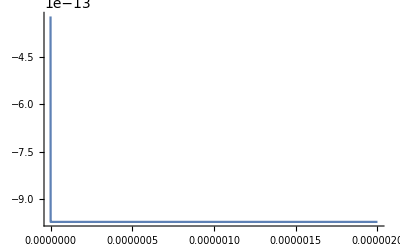

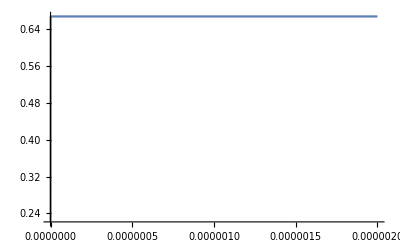

```mathematica
spont[t_] :=( (5α)/36 n4[t] + (2α)/9 n5[t]+α/4 n3[t] + α/9 n4[t]+α/36 n5[t])/.sol;
Plot[spont[t], {t, 0, tp}]
Plot[(n3[t]+n4[t]+n5[t])/.sol, {t, 0, tp}]

(*nmean[ν_]:=NIntegrate[spont[t]/.sol[ν], {t, 0, tp}];
DiscretePlot[nmean[ν], {ν, -1 10^6-a1, 1 10^6-a1, 10^4}]*)
(*Plot[spont[t],{t, 0, tp}, PlotRange->Full, PlotStyle->Blue]*)
```

```mathematica
Show[%714,Axes->False]
```

```mathematica
κ = NIntegrate[spont[t], {t, 0, tp}]^-1
```

{0.666666}

```mathematica
{0.6666658672280258}
```

[atoms/sec] = 1/κ[photons/sec]

### Expected number of atoms per second

Pressure P in [torr], temperature T in [K]

```mathematica
Clear[P, n0, k, m, vavg, a, θ, As, Temp,dN, Natoms];

P[T_] :=10^(10.3454 -8345.57/T-8.84 10^-5 T - 0.68196 Log10[T]) 
n0[T_]:=9.66 10^(18+6)P[T]/T
k = 1.38 10^-23;
m = 6.015 1.66 10^-27;
vavg[T_]:=√((8 k T)/(π m))
θ=4/220;
As= (π(8 10^-3)^2)/4;
a[T_]:= √((2 k T)/m)
```

#### Natoms[atoms/sec] in a collimation angle 2θ

Account for different atom-laser interaction time for different velocities in z-direction doesn’t change the coefficient κ

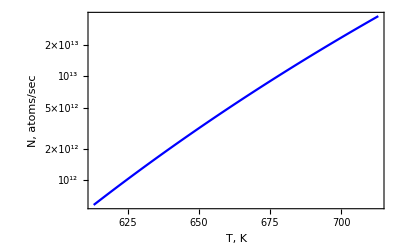

```mathematica
Natoms[Temp_] := Integrate[(2 n0[Temp] As)/(√π a[Temp]^3)vr ⅇ^(-(vr/a[Temp])^2)vz ⅇ^(-(vz/a[Temp])^2), {vz, 0, ∞}, {vr, 0, θ vz}]
LogPlot[Natoms[Temp], {Temp, 340+273, 440+273}, PlotRange->Full,Frame->True, FrameLabel->{"T, K", "N, atoms/sec"}, PlotStyle->Blue]
```

```mathematica
Natoms[300+273]
```

7.02392×10^10

Converges for total number of atoms flying out of the oven

```mathematica
Integrate[dN[vr, vz], {vz, 0, ∞}, {vr, 0, ∞}]
(n0[Temp]vavg[Temp] As)/4

Clean[W, Temp, koef];
W = 2 10^-3;
Temp = 440+273;
```

∫_0^∞ ∫_0^∞ dN[vr,vz]ⅆvrⅆvz

1.15529×10^17

```mathematica
koef[T_] := NIntegrate[vz ⅇ^(-(vz/a[T])^2) spont[t],{vz, 300, ∞}, {t, 0,W/vz }]/NIntegrate[vz ⅇ^(-(vz/a[T])^2) , {vz, 0, ∞}]; 
koef[Temp]
```

{1.42667}

```mathematica
15 10^-9/(h ν)koef[440+237]
```

{7.21753×10^10}

For total power of fluorescence P from all atoms ~ 15nW number of atoms N=κ P/hν=7.2 *10^10, expected - 3.8*10^13, which is ~500N

### Solid angle coefficient

```mathematica
h = 90
d = 42.2
Ω=2π (1- h/(√(h^2+(d/2)^2)))
β=Ω/(4π)
```

90

42.2

0.165868

0.0131994